```mathematica
M=10
m=1
g=10
l=100
```

10

1

10

100

```mathematica
MASS  IN  A  TUBE ::
```

```mathematica
L=1/2 1/3 M*l^2*(θ'[t])^2+1/2 m(x'[t])^2+1/2 m*(x[t])^2*(θ'[t])^2+(M*g*l)/2 Sin[θ[t]]+m*g*x[t]*Sin[θ[t]]
```

5000 Sin[θ[t]]+10 Sin[θ[t]] x[t]+1/2 x'[t]^2+50000/3 θ'[t]^2+1/2 x[t]^2 θ'[t]^2

```mathematica
D[(D[L,x'[t]]), t]-D[L,x[t]]
```

-10 Sin[θ[t]]-x[t] θ'[t]^2+x''[t]

```mathematica
D[(D[L,θ'[t]]), t]-D[L,θ[t]]
```

-5000 Cos[θ[t]]-10 Cos[θ[t]] x[t]+2 x[t] x'[t] θ'[t]+(100000 θ''[t])/3+x[t]^2 θ''[t]

{-10 Sin[θ[t]]-x[t] θ'[t]^2+x''[t]==0,-5000 Cos[θ[t]]-10 Cos[θ[t]] x[t]+2 x[t] x'[t] θ'[t]+(100000 θ''[t])/3+x[t]^2 θ''[t]==0}

{x[0]==0,x'[0]==0,θ[0]==0,θ'[0]==0}

{{x→InterpolatingFunction[…],θ→InterpolatingFunction[…]}}

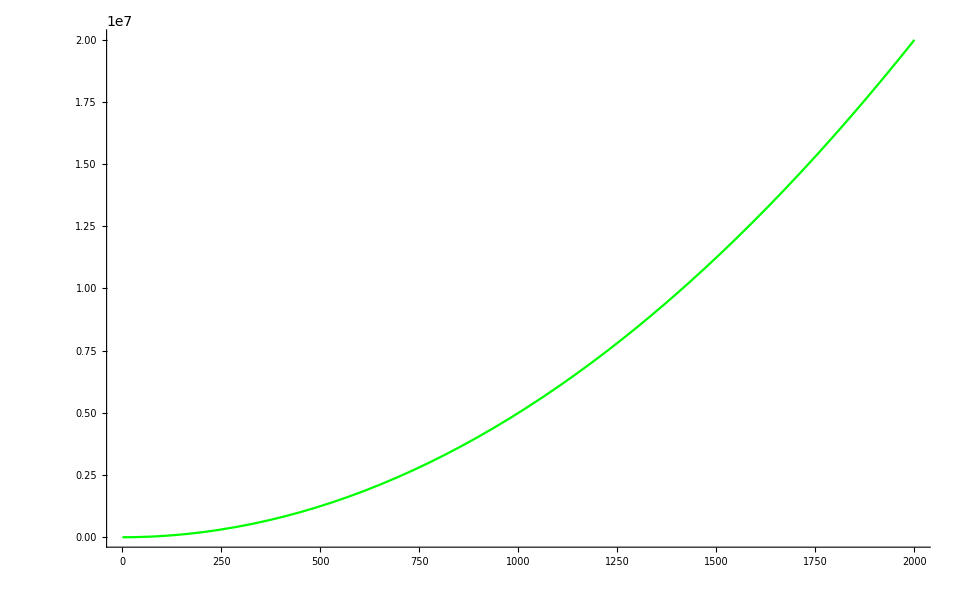

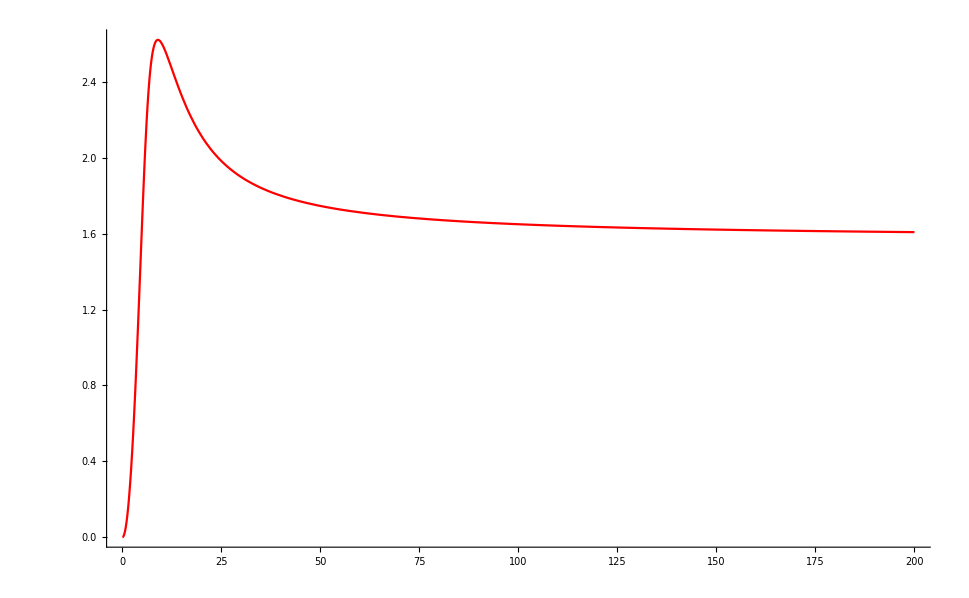

```mathematica
s={-10 Sin[θ[t]]-x[t] θ'[t]^2+x''[t]== 0,
-5000 Cos[θ[t]]-10 Cos[θ[t]] x[t]+2 x[t] x'[t] θ'[t]+(100000 θ''[t])/3+x[t]^2 θ''[t]==0}
ics={x[0]== 0,x'[0]== 0,θ[0]== 0,θ'[0]== 0}
sol=NDSolve[{s,ics},{x,θ},{t,0,2000}]
Plot[Evaluate[x[t]/.sol],{t,0,2000},PlotRange->All,PlotStyle->Green]
Plot[Evaluate[θ[t]/.sol],{t,0,200},PlotRange->All,PlotStyle->Red]
```

INVERTED  PENDULUM::

```mathematica
ω=200
```

200

```mathematica
L1=1/2 m*(l^2*(θ'[t])^2+(2*ω*Sin[ω*t])^2-2*l*(2*ω*Sin[ω*t])*θ'[t]*Sin[θ[t]])-m*g*(2*Cos[ω*t]+l*Cos[θ[t]])
D[(D[L1,θ'[t]]), t]-D[L1,θ[t]]
```

-10 (2 Cos[200 t]+100 Cos[θ[t]])+1/2 (160000 Sin[200 t]^2-80000 Sin[200 t] Sin[θ[t]] θ'[t]+10000 θ'[t]^2)

-1000 Sin[θ[t]]+40000 Cos[θ[t]] Sin[200 t] θ'[t]+1/2 (-16000000 Cos[200 t] Sin[θ[t]]-80000 Cos[θ[t]] Sin[200 t] θ'[t]+20000 θ''[t])

{-1000 Sin[θ[t]]+40000 Cos[θ[t]] Sin[200 t] θ'[t]+1/2 (-16000000 Cos[200 t] Sin[θ[t]]-80000 Cos[θ[t]] Sin[200 t] θ'[t]+20000 θ''[t])==0}

{θ[0]==0.11,θ'[0]==-0.1}

{{θ→InterpolatingFunction[{{0., 200.}}, <>]}}

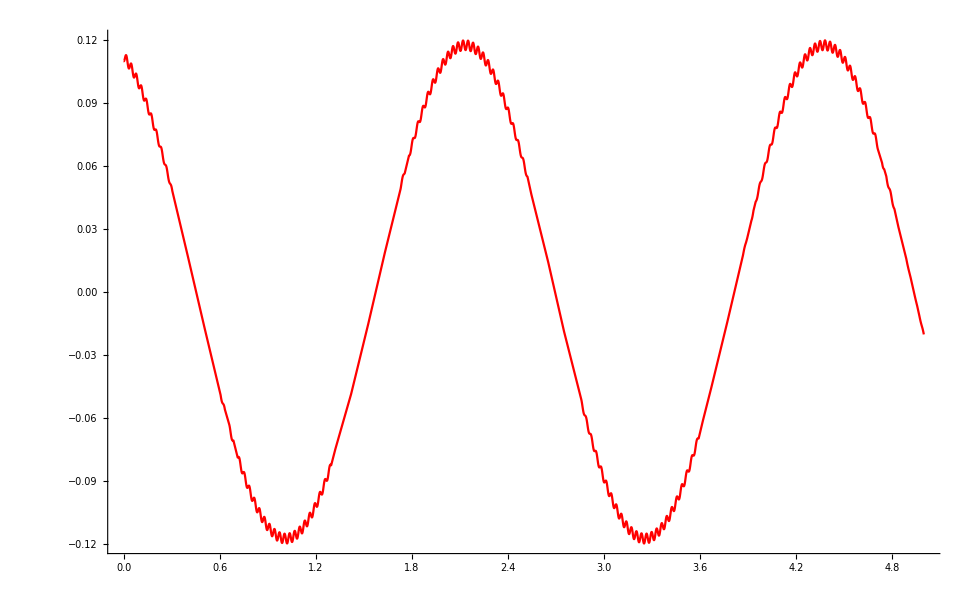

```mathematica
s1={D[(D[L1,θ'[t]]), t]-D[L1,θ[t]]==0}
ics={θ[0]== 0.11,θ'[0]== -0.1}
sol1=NDSolve[{s1,ics},{θ},{t,0,200}]
Plot[Evaluate[θ[t]/.sol1],{t,0,5},PlotRange->All,PlotStyle->Red]
```

```mathematica
ROTATING CURVE:  MORIN PROBLEM   6.17:

λ=10
b=2
a=1
y[x_]:=b*(x/a)^λ
Subscript[x, 0]=a(a^2 ω^2/(λ*g*b))^(1/(λ-2))
y'[x]
L2=1/2 m*(ω^2*(x[t])^2+(x'[t])^2*(1+((λ*b *(x[t])^(λ-1))/a^3)^2))-m*g*b*(x[t]/a)^λ
D[(D[L2,x'[t]]), t]-D[L2,x[t]]
```

10

2

1

2^(3/8) 5^(1/4)

20 x^9

-20 x[t]^10+1/2 (40000 x[t]^2+(1+400 x[t]^18) x'[t]^2)

200 x[t]^9+7200 x[t]^17 x'[t]^2+1/2 (-80000 x[t]-7200 x[t]^17 x'[t]^2)+(1+400 x[t]^18) x''[t]

{200 x[t]^9+7200 x[t]^17 x'[t]^2+1/2 (-80000 x[t]-7200 x[t]^17 x'[t]^2)+(1+400 x[t]^18) x''[t]==0}

{x[0]==1.93933,x'[0]==0.}

{{x→InterpolatingFunction[…]}}

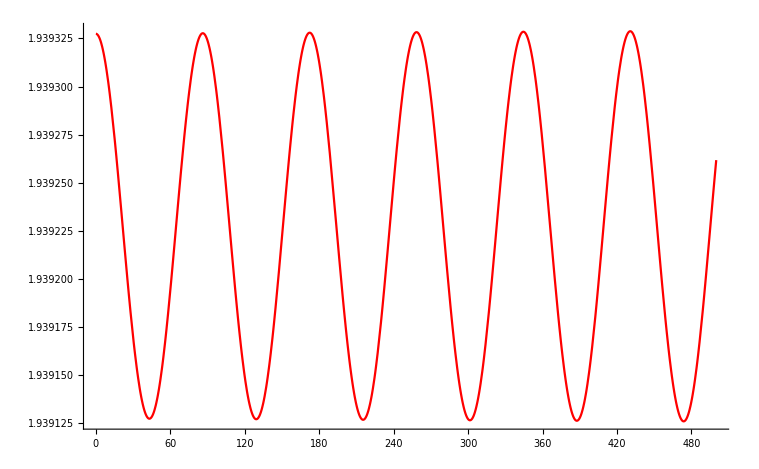

```mathematica
s2={200 x[t]^9+7200 x[t]^17 x'[t]^2+1/2 (-80000 x[t]-7200 x[t]^17 x'[t]^2)+(1+400 x[t]^18) x''[t]==0}
ics2={x[0]== Subscript[x, 0]+0.0001,x'[0]== 0.0}
sol2=NDSolve[{s2,ics2},{x},{t,0,5000}]
Plot[Evaluate[x[t]/.sol2],{t,0,500},PlotRange->All,PlotStyle->Red]
```